```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./tmp.dat","Table"]
```

{{#,L[fm^-1],C_0[nucl]},{4,-505.15},{6,-1090.55},{8,-1898.7},{10,-2934.2}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+lam^2))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]];
norm=Compile[{b1,b2},(Pi/(2 b1+2 b2))^(3/2)];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2)),{i,Length[core]},{j,Length[core]}]]])^2];

VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh,no},Block[{eta2,eta3,w2,w3},
eta2=(*(8/Pi^1.5) ((Aa+Bb) (Gg+Hh))^1.5*)(π^(3/2)/4) Cc/(lam Bb+Aa (lam+2 Gg+2 Bb)+lam Hh+2 Bb Hh+Gg (lam+2 Hh))^(3/2);
w2=2 lam (Aa+Hh) (Gg+Bb)/(lam Bb+Aa (lam+2 Gg+2 Bb)+lam Hh+2 Bb Hh+Gg (lam+2 Hh));
eta3=(*(8/Pi^1.5) ((Aa+Bb) (Gg+Hh))^1.5*)(π^(3/2)/4) Cc/(lam Bb+Gg (lam+2 Bb)+lam Hh+2 Bb Hh+Aa (lam+2 Gg+2 Hh))^(3/2);
w3=2 lam (Aa+Bb) (Gg+Hh)/(lam Bb+Gg (lam+2 Bb)+lam Hh+2 Bb Hh+Aa (lam+2 Gg+2 Hh));
(eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2])
(*Cc Exp[-lam^2/4 r^2] no*)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

Do[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],1.],{i,1,Npoints}]];

Wmat=Wmat+cij amat;

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

```mathematica
dCores6={{-2.08286,{{-0.0698831,0.071760}, {-0.227762, 0.48182}, {-0.534198,3.0238}, {-0.811094, 13.460}}},
{-2.03348,{{-0.103955, 0.10433}, {-0.276241, 0.70890}, {-0.610444,3.9917}, {-0.735012, 16.055}}},
{-2.05877,{{-0.107951, 0.10108}, {-0.277921, 0.69288}, {-0.571931,3.5121}, {-0.757815, 13.787}, {-0.098584, 22.437}}},
{-2.05122,{{-0.0668923, 0.055875}, {-0.258185, 0.52526}, {-0.484909,2.8672}, {-0.0737611, 6.5017}, {-0.829632, 13.273}}}};
dCores4={{-2.08725,{{-0.06287097147752445,0.0509347915649414077`5.},{-0.1868644625347115,0.2384193420410156264`5.}, {-0.5732408737863257,1.3635551452636718763`5.}, {-0.7953136577525721,7.250524330139160157`5.}}},
{-2.10116,{{0.148864, 0.087665}, {0.385882, 0.61862}, {0.570137,   2.4742}, {0.709844, 7.3577}}},
{-2.08286,{{-0.129864, 0.075504}, {-0.426576, 0.56242}, {-0.808166,   3.2751}, {-0.3607, 7.6785}, {-0.133911, 19.048}}}
};
λ=6;
dCores=dCores6;
```

```mathematica
LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
dCoresB={};
Do[
wi=dCores[[mm]][[2]][[All,2]];
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];
Print["TemplateBox[<|\"boxes\" -> FormBox[StyleBox[\"H\", \"TI\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"H\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"] = ",hamm//MatrixForm,"             TemplateBox[<|\"boxes\" -> FormBox[StyleBox[\"N\", \"TI\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"N\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"] = ",normm//MatrixForm,"\n now transform to a unit-norm basis:"];

{evaln,evecn}=Eigensystem[normm];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;

{evalg,evecg}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[evalg]];
eigsortedg=Re[evalg[[ord]]];
evecsg=evecg[[ord]];
Print[{eigsortedg[[1]],evecsg[[1]]}];
Norm[evecsg[[1]]];
(*Print[dCores[[mm]][[2]],Transpose[{evecsg[[1]],wi}]];*)

{eval,evec}=Eigensystem[Transpose[fulltrafo].hamm.fulltrafo];
(*Print[{eval,evec}];*)
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
evecs=evec[[ord]];
Print[{eigsorted[[1]],evecs[[1]]}];
Norm[evecs[[1]]];
AppendTo[dCoresB,{eigsortedg[[1]],Transpose[{evecsg[[1]],wi}]}];
(*AppendTo[dCoresB,{eigsorted[[1]],Transpose[{evecs[[1]],wi}]}];*)
,{mm,Length[dCores]}];
```

= (133.863 | 10.2794 | -19.0059 | -11.7743
10.2794 | 36.3835 | -6.0181 | -9.70405
-19.0059 | -6.0181 | 6.69521 | -1.56526
-11.7743 | -9.70405 | -1.56526 | 4.67133)              = (36.2086 | 4.77979 | 0.361469 | 0.0395502
4.77979 | 2.08117 | 0.299939 | 0.0378182
0.361469 | 0.299939 | 0.132375 | 0.0294167
0.0395502 | 0.0378182 | 0.0294167 | 0.0140951)
 now transform to a unit-norm basis:

{-2.08296,{-0.0698815,-0.22776,-0.534191,-0.811099}}

{-2.08296,{0.820163,0.505018,-0.26125,0.0635465}}

= (106.427 | 4.06574 | -17.6664 | -10.3629
4.06574 | 26.3374 | -5.38155 | -8.0516
-17.6664 | -5.38155 | 5.46313 | -0.424104
-10.3629 | -8.0516 | -0.424104 | 4.75417)              = (20.6548 | 2.68448 | 0.237484 | 0.0303071
2.68448 | 1.16616 | 0.193175 | 0.0286825
0.237484 | 0.193175 | 0.0872766 | 0.0219339
0.0303071 | 0.0286825 | 0.0219339 | 0.0108198)
 now transform to a unit-norm basis:

{-2.03357,{-0.103955,-0.276233,-0.610448,-0.735012}}

{-2.03357,{0.855837,-0.465602,0.221514,-0.0411025}}

= (108.55 | 4.1912 | -17.863 | -11.448 | -8.08786
4.1912 | 26.8664 | -4.07917 | -8.6657 | -6.65933
-17.863 | -4.07917 | 5.95471 | -0.708062 | -1.74156
-11.448 | -8.6657 | -0.708062 | 4.68347 | 4.21743
-8.08786 | -6.65933 | -1.74156 | 4.21743 | 4.83505)              = (21.6589 | 2.7828 | 0.286646 | 0.0380379 | 0.0183994
2.7828 | 1.20683 | 0.228315 | 0.0357299 | 0.0176978
0.286646 | 0.228315 | 0.105751 | 0.0273618 | 0.0148935
0.0380379 | 0.0357299 | 0.0273618 | 0.0135966 | 0.00902995
0.0183994 | 0.0176978 | 0.0148935 | 0.00902995 | 0.00654919)
 now transform to a unit-norm basis:

{-2.05889,{-0.107949,-0.277929,-0.571938,-0.757802,-0.0986155}}

{-2.05889,{0.854235,-0.468897,0.221165,-0.038317,-0.00597499}}

= (155.331 | 1.11867 | -19.7467 | -16.8339 | -11.9635
1.11867 | 33.9259 | -4.2959 | -10.7572 | -9.55881
-19.7467 | -4.2959 | 7.00464 | 2.0009 | -1.85587
-16.8339 | -10.7572 | 2.0009 | 4.54501 | 2.90865
-11.9635 | -9.55881 | -1.85587 | 2.90865 | 4.66418)              = (52.6997 | 4.4439 | 0.393931 | 0.117237 | 0.0404566
4.4439 | 1.82841 | 0.31507 | 0.105689 | 0.0384099
0.393931 | 0.31507 | 0.143367 | 0.068651 | 0.030361
0.117237 | 0.105689 | 0.068651 | 0.041985 | 0.022388
0.0404566 | 0.0384099 | 0.030361 | 0.022388 | 0.014394)
 now transform to a unit-norm basis:

{-2.05131,{-0.0668896,-0.258179,-0.484902,-0.0737318,-0.829641}}

{-2.05131,{0.805536,-0.540216,0.239308,-0.041563,0.0168293}}

Obtain dimer-dimer scattering length for the core ensemble

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.0001;
(* Integration grid *)
rMa=6;
grdPerFermi=165;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

nbrOfCores=Length[dCoresB];
Print["core  λ   LEC      R_max   N # points    E_match    B_dimer      Basis Dim.    a_dd"];
Do[
{e0Core,dimerCore}=dCoresB[[nn]];

dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
tmp=GetEREP3[λ^2/4,rMa,nGrd,dimerCore,LECc,energ];
AppendTo[results,{λ,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print[nn,")    ",λ,"   ",LECc,"   ",rMa,"    ",nGrd,"           ",energ,"     ",e0Core,"   ",dimCore,"             ",tmp];
,{nn,Length[dCoresB]}];
```

core  λ   LEC      R_max   N # points    E_match    B_dimer      Basis Dim.    a_dd

1)    6   -1090.55   6    990           0.0001     -2.08296   4             1.20716

2)    6   -1090.55   6    990           0.0001     -2.03357   4             1.0422

3)    6   -1090.55   6    990           0.0001     -2.05889   5             1.05682

4)    6   -1090.55   6    990           0.0001     -2.05131   5             1.37363

```mathematica
NormTFt[core_]:=(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2))),{i,Length[core]},{j,Length[core]}]]])^2;
```

```mathematica
aa=dCoresB[[1]][[2]];
num=(NIntegrate[r^2 (Total[#[[1]] Exp[-#[[2]] r^2]&/@aa])^2,{r,0,1000}])^2
ana=NormTF[aa]
num/ana
```

0.0199735

0.0199735

1.

Results core 1 :  Norm: 50.0663   a_dd = 1.22456

Results core 2 :  Norm: 48.8013   a_dd = 1.04809

Results core 3 :  Norm: 38.892   a_dd = 1.06369

Results core 4 :  Norm: 38.3279   a_dd = 1.41431

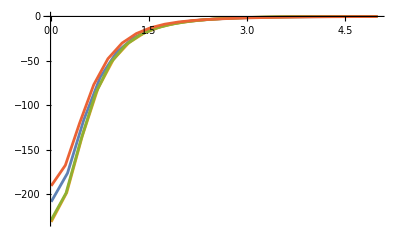

```mathematica
energ=0.0001;

(* Integration grid *)
rMa=5.;
grdPerFermi=185;
nGrd=IntegerPart[rMa grdPerFermi];
LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
(* Plot parameters for the visualization of V(r,r') *)
nR=20;rMi=0.01;thresh=10^-0;

pots={};
Do[
{e0Core,dimerCore}=dCoresB[[nn]];(*ApproxDimerWF[lambd,dimDimer,nparallelThreads,nDimerWidthSamples,minDimerWidth,maxDimerWidth,midWidthdiff,0];*)

normCore=1./NormTF[dimerCore];
dimCore=Length[dimerCore];


tmp=GetEREP3[λ^2/4,rMa,nGrd,dimerCore,LECc,energ];
Print["Results core ",nn," :  Norm: ",normCore,"   a_dd = "<>ToString[tmp]];

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];
potloc={};
ttp=0;
Do[
cij=dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]] normCore;

potloctmp=
Table[{rR[[i]],cij VlocTF[rR[[i]],λ^2/4,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],1]}
,{i,Length[rR]}];
AppendTo[potloc,potloctmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}];

AppendTo[pots,Transpose[{potloc[[1]][[All,1]],Total[potloc[[All,All,2]]]}]];

,{nn,Length[dCoresB]}];
ListPlot[pots,Joined->True,PlotRange->Full]
```

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

λ = 6   C_0(λ) = -1090.55     R_max = 1.2     #(grid points) = 60                a_dd = 1.42152 fm        a_dd/a_aa = 0.314772

λ = 6   C_0(λ) = -1090.55     R_max = 2.11     #(grid points) = 105                a_dd = 1.37168 fm        a_dd/a_aa = 0.303736

λ = 6   C_0(λ) = -1090.55     R_max = 3.02     #(grid points) = 151                a_dd = 1.19902 fm        a_dd/a_aa = 0.265503

λ = 6   C_0(λ) = -1090.55     R_max = 3.93     #(grid points) = 196                a_dd = 1.0852 fm        a_dd/a_aa = 0.240299

λ = 6   C_0(λ) = -1090.55     R_max = 4.84     #(grid points) = 242                a_dd = 1.04985 fm        a_dd/a_aa = 0.232473

λ = 6   C_0(λ) = -1090.55     R_max = 5.75     #(grid points) = 287                a_dd = 1.04228 fm        a_dd/a_aa = 0.230796

λ = 6   C_0(λ) = -1090.55     R_max = 6.66     #(grid points) = 333                a_dd = 1.04105 fm        a_dd/a_aa = 0.230523

λ = 6   C_0(λ) = -1090.55     R_max = 7.57     #(grid points) = 378                a_dd = 1.0409 fm        a_dd/a_aa = 0.23049

λ = 6   C_0(λ) = -1090.55     R_max = 8.48     #(grid points) = 424                a_dd = 1.04089 fm        a_dd/a_aa = 0.230488

λ = 6   C_0(λ) = -1090.55     R_max = 9.39     #(grid points) = 469                a_dd = 1.04089 fm        a_dd/a_aa = 0.230488

λ = 6   C_0(λ) = -1090.55     R_max = 10.3     #(grid points) = 515                a_dd = 1.04089 fm        a_dd/a_aa = 0.230488

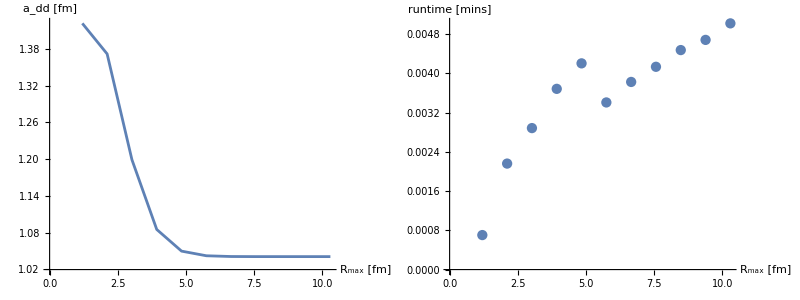

```mathematica
rMaxStart=1.2;
rMaxEnd=10.3;
nbrR=10;

{e0Core,dimerCore}=dCoresB[[2]];
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=50;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[λ^2/4,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",λ,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```